```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,5.55701×10^7},{60,5.55087×10^7},{70,5.50317×10^7},{80,5.35235×10^7},{90,5.2681×10^7},{100,5.18181×10^7},{110,5.09752×10^7},{120,5.01735×10^7},{130,4.80746×10^7},{140,4.73778×10^7},{150,4.67236×10^7},{160,4.60911×10^7},{170,4.55328×10^7},{180,4.49778×10^7},{190,4.44652×10^7},{200,4.39824×10^7},{210,4.3831×10^7},{220,4.35853×10^7},{230,4.31754×10^7},{240,4.27763×10^7},{250,4.23937×10^7},{260,4.2034×10^7},{270,4.23741×10^7},{280,4.20415×10^7},{290,4.17239×10^7},{300,4.14181×10^7},{310,4.08242×10^7},{320,3.90546×10^7},{330,3.87975×10^7},{340,3.85473×10^7},{350,3.80442×10^7},{360,3.75908×10^7},{370,3.62854×10^7},{380,3.60797×10^7},{390,3.56036×10^7},{400,3.53903×10^7},{410,3.50561×10^7},{420,3.45873×10^7},{430,3.42523×10^7},{440,3.31128×10^7},{450,3.29431×10^7},{460,3.2779×10^7},{470,3.26154×10^7},{480,3.24593×10^7},{490,3.16806×10^7},{500,3.14478×10^7},{510,3.13191×10^7},{520,3.09754×10^7},{530,3.08538×10^7},{540,3.07366×10^7},{550,2.98078×10^7},{560,2.96906×10^7},{570,2.95761×10^7},{580,2.9451×10^7},{590,2.93556×10^7},{600,2.92867×10^7},{610,2.91816×10^7},{620,2.91405×10^7},{630,2.90342×10^7},{640,2.8814×10^7},{650,2.87163×10^7},{660,2.86511×10^7},{670,2.85919×10^7},{680,2.81457×10^7},{690,2.80623×10^7},{700,2.79816×10^7},{710,2.78104×10^7},{720,2.77356×10^7},{730,2.76624×10^7},{740,2.76003×10^7},{750,2.66097×10^7},{760,2.65378×10^7},{770,2.62754×10^7},{780,2.62435×10^7},{790,2.61758×10^7},{800,2.61087×10^7},{810,2.59068×10^7},{820,2.58513×10^7},{830,2.57923×10^7},{840,2.57374×10^7},{850,2.56592×10^7},{860,2.55859×10^7},{870,2.55333×10^7},{880,2.54808×10^7},{890,2.54585×10^7},{900,2.54058×10^7},{910,2.53539×10^7},{920,2.53026×10^7},{930,2.52518×10^7},{940,2.52017×10^7},{950,2.5152×10^7},{960,2.51029×10^7},{970,2.50541×10^7},{980,2.50058×10^7},{990,2.49632×10^7},{1000,2.4916×10^7},{1010,2.48691×10^7},{1020,2.49182×10^7},{1030,2.4874×10^7},{1040,2.48299×10^7},{1050,2.47861×10^7},{1060,2.47424×10^7},{1070,2.46988×10^7},{1080,2.46553×10^7},{1090,2.46119×10^7},{1100,2.45685×10^7},{1110,2.4525×10^7},{1120,2.44578×10^7},{1130,2.44138×10^7},{1140,2.43656×10^7},{1150,2.43334×10^7},{1160,2.43094×10^7},{1170,2.42641×10^7},{1180,2.42188×10^7},{1190,2.41717×10^7},{1200,2.42669×10^7},{1210,2.42271×10^7},{1220,2.41855×10^7},{1230,2.41509×10^7},{1240,2.45173×10^7},{1250,2.44804×10^7},{1260,2.53108×10^7},{1270,2.53017×10^7},{1280,2.52638×10^7},{1290,2.52253×10^7},{1300,2.53453×10^7},{1310,2.53078×10^7},{1320,2.52687×10^7},{1330,2.56028×10^7},{1340,2.55944×10^7},{1350,2.58925×10^7},{1360,2.58618×10^7},{1370,2.58603×10^7},{1380,2.58268×10^7},{1390,2.56203×10^7},{1400,2.55782×10^7},{1410,2.55476×10^7},{1420,2.54891×10^7},{1430,2.54575×10^7},{1440,2.54094×10^7},{1450,2.53593×10^7},{1460,2.62686×10^7},{1470,2.62126×10^7},{1480,2.61545×10^7},{1490,2.63728×10^7},{1500,2.63095×10^7},{1510,2.63475×10^7},{1520,2.63962×10^7},{1530,2.63191×10^7},{1540,2.62367×10^7},{1550,2.61514×10^7},{1560,2.6058×10^7},{1570,2.75994×10^7},{1580,2.82138×10^7},{1590,2.83364×10^7},{1600,2.81717×10^7},{1610,2.80774×10^7},{1620,2.71999×10^7},{1630,2.65236×10^7},{1640,2.81925×10^7},{1650,2.79849×10^7},{1660,2.82763×10^7},{1670,2.80896×10^7},{1680,2.79055×10^7},{1690,2.9357×10^7},{1700,2.83156×10^7},{1710,2.80624×10^7},{1720,2.77933×10^7},{1730,2.75096×10^7},{1740,2.66694×10^7},{1750,2.63475×10^7}}

{{50,555.701},{60,555.087},{70,550.317},{80,535.235},{90,526.81},{100,518.181},{110,509.752},{120,501.735},{130,480.746},{140,473.778},{150,467.236},{160,460.911},{170,455.328},{180,449.778},{190,444.652},{200,439.824},{210,438.31},{220,435.853},{230,431.754},{240,427.763},{250,423.937},{260,420.34},{270,423.741},{280,420.415},{290,417.239},{300,414.181},{310,408.242},{320,390.546},{330,387.975},{340,385.473},{350,380.442},{360,375.908},{370,362.854},{380,360.797},{390,356.036},{400,353.903},{410,350.561},{420,345.873},{430,342.523},{440,331.128},{450,329.431},{460,327.79},{470,326.154},{480,324.593},{490,316.806},{500,314.478},{510,313.191},{520,309.754},{530,308.538},{540,307.366},{550,298.078},{560,296.906},{570,295.761},{580,294.51},{590,293.556},{600,292.867},{610,291.816},{620,291.405},{630,290.342},{640,288.14},{650,287.163},{660,286.511},{670,285.919},{680,281.457},{690,280.623},{700,279.816},{710,278.104},{720,277.356},{730,276.624},{740,276.003},{750,266.097},{760,265.378},{770,262.754},{780,262.435},{790,261.758},{800,261.087},{810,259.068},{820,258.513},{830,257.923},{840,257.374},{850,256.592},{860,255.859},{870,255.333},{880,254.808},{890,254.585},{900,254.058},{910,253.539},{920,253.026},{930,252.518},{940,252.017},{950,251.52},{960,251.029},{970,250.541},{980,250.058},{990,249.632},{1000,249.16},{1010,248.691},{1020,249.182},{1030,248.74},{1040,248.299},{1050,247.861},{1060,247.424},{1070,246.988},{1080,246.553},{1090,246.119},{1100,245.685},{1110,245.25},{1120,244.578},{1130,244.138},{1140,243.656},{1150,243.334},{1160,243.094},{1170,242.641},{1180,242.188},{1190,241.717},{1200,242.669},{1210,242.271},{1220,241.855},{1230,241.509},{1240,245.173},{1250,244.804},{1260,253.108},{1270,253.017},{1280,252.638},{1290,252.253},{1300,253.453},{1310,253.078},{1320,252.687},{1330,256.028},{1340,255.944},{1350,258.925},{1360,258.618},{1370,258.603},{1380,258.268},{1390,256.203},{1400,255.782},{1410,255.476},{1420,254.891},{1430,254.575},{1440,254.094},{1450,253.593},{1460,262.686},{1470,262.126},{1480,261.545},{1490,263.728},{1500,263.095},{1510,263.475},{1520,263.962},{1530,263.191},{1540,262.367},{1550,261.514},{1560,260.58},{1570,275.994},{1580,282.138},{1590,283.364},{1600,281.717},{1610,280.774},{1620,271.999},{1630,265.236},{1640,281.925},{1650,279.849},{1660,282.763},{1670,280.896},{1680,279.055},{1690,293.57},{1700,283.156},{1710,280.624},{1720,277.933},{1730,275.096},{1740,266.694},{1750,263.475}}

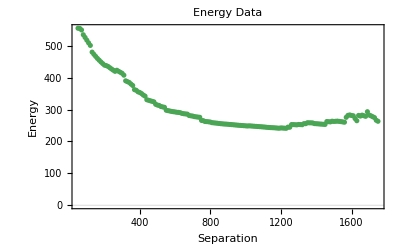

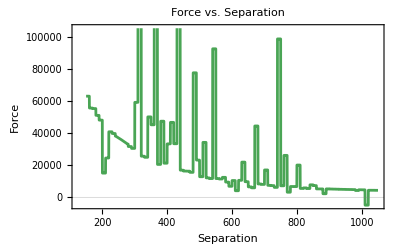

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

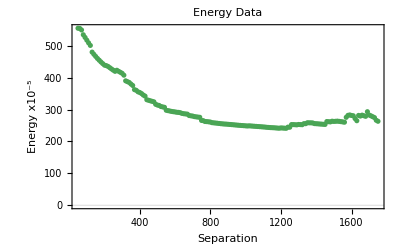

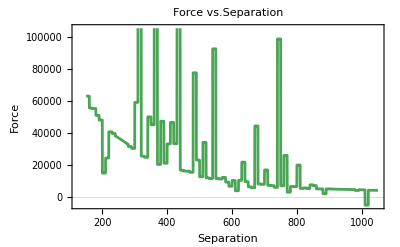

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
|
```